# Unsupervised Clustering on whole dataset (Principal Component)

```mathematica
fullReducedDataset = Join[reducedOxyNo80[[All,1]],reducedOxyYes80[[All,1]]];
```

```mathematica
clusterAutomatic = FindClusters[fullReducedDataset,Method->"MeanShift"];
```

```mathematica
clusterAutomatic//Dimensions
```

{12}

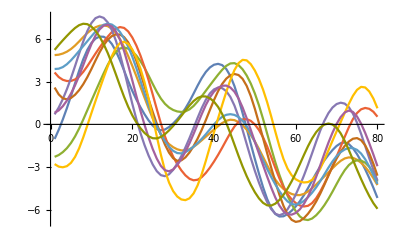
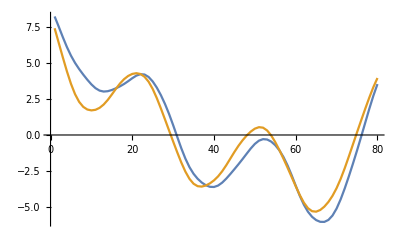
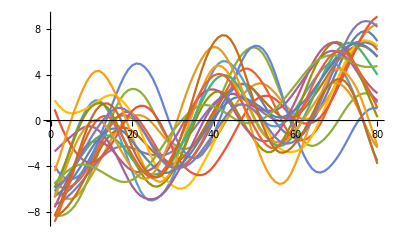
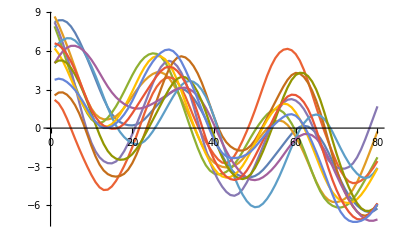
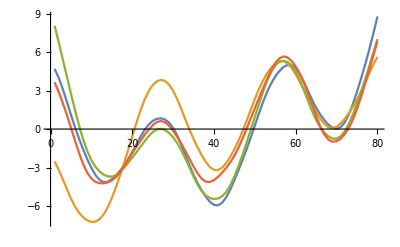
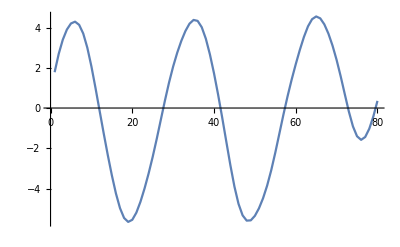
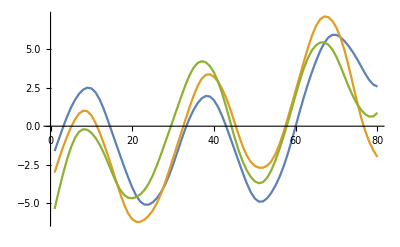
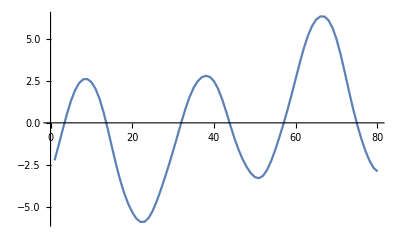
{-Graphics-→10,-Graphics-→2,-Graphics-→21,-Graphics-→12,-Graphics-→4,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1}

```mathematica
Table[ListLinePlot[clusterAutomatic[[i]]]-> Length[clusterAutomatic[[i]]],{i,Length@clusterAutomatic}]
```

```mathematica
10+12+21+3+2
```

48

```mathematica
%/60
```

4/5

```mathematica
%//N
```

0.8

# Unsupervised Clustering on whole dataset (Second Principal Component)

```mathematica
clusterAutomaticSecond = Join[reducedOxyNo80[[All,2]],reducedOxyYes80[[All,2]]];
```

```mathematica
clusterAutomaticSecond = FindClusters[clusterAutomaticSecond,Method->"MeanShift"];
```

```mathematica
clusterAutomaticSecond//Dimensions
```

{2}

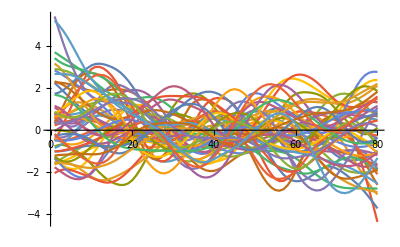
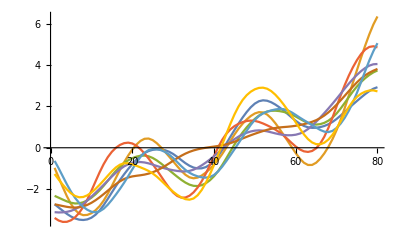
{-Graphics-→52,-Graphics-→8}

```mathematica
Table[ListLinePlot[clusterAutomaticSecond[[i]]]-> Length[clusterAutomaticSecond[[i]]],{i,Length@clusterAutomaticSecond}]
```